## Рублевская Екатерина Александровна гр. 321702 Вариант 13 Лабораторная работа №2

### Задание 1: -Graphics- -Graphics-

```mathematica
f[x_]=36*x^3-168*x^2+55*x+350;
```

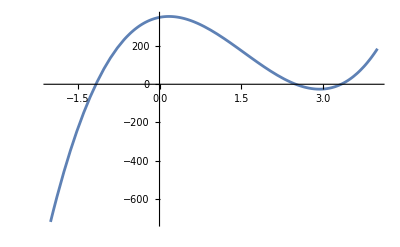

```mathematica
Plot[f[x],{x,-2,4},AxesOrigin->{0,0}]
```

По графику видно, что уравнение имеет три действительных корня . Они
расположены в интервалах (-2, -1), (2, 3), (3, 4)

МЕТОД ХОРД

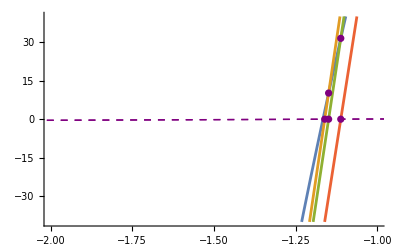

Решение х= -1.16614 Шаг= 5

```mathematica
a=-2;
b= -1;

eps=0.001;
ex=eps*10;
If [ f[a]*f''[a]>0,
xn0=b; g[x_]:=a- (f[a]*(x-a)/(f[x]-f[a])); 
hord [x_,xn_]:=f[xn]+((x-xn)/(xn-a)*(f[xn]-f[a])),

xn0=a;g[x_]:=x-(f[x]*(b-x)/(f[b]-f[x]));  
hord [x_,xn_]:=f[xn]+((x-xn)/(xn-b)*(f[xn]-f[b]))];

xn1=g[xn0]; n=1;

While [ex>eps,
If [n==2,
Print [Plot [{f[x],hord[x,xn1],hord[x,xn0],hord[x,xn01]},{x,a,b},Epilog->{Purple,Dashed,InfiniteLine[{xn1,0},{-2,-1}],InfiniteLine[{xn0,0},{-2,-1}],PointSize[0.013],Point[{{xn0,0},{xn0,f[xn0]},{xn1,0},{xn1,f[xn1]},{g[xn1],0}}]},PlotRange->40]]
];
xn01=xn0;xn0=xn1;
xn1=g[xn0];
ex=((xn1-xn0)^2)/(Abs[xn1+xn01-2xn0]);
n=n+1;
]
Print["Решение х= ",xn1//N," Шаг= ",n]
```

### Задание 2: -Graphics- -Graphics-

```mathematica
f[x_]=x^6+4*x^5-10x^4-24*x^3+13*x^2+44*x+20;
```

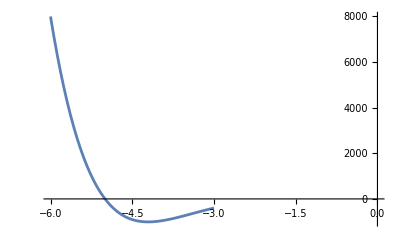

```mathematica
Plot[f[x], {x,-6,-3}, AxesOrigin->{0,0}]
```

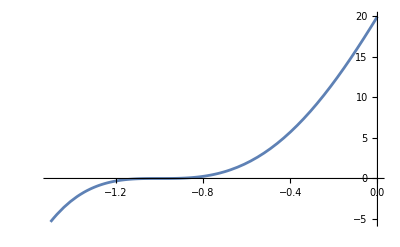

```mathematica
Plot[f[x], {x,-1.5,0}, AxesOrigin->{0,0}]
```

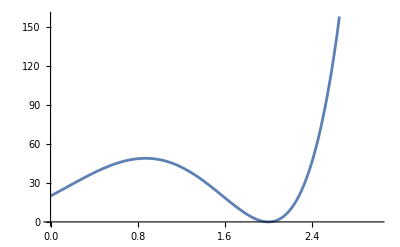

```mathematica
Plot[f[x], {x,0,3}, AxesOrigin->{0,0}]
```

Корни находятся на промежутках (-5.5, -4.7) (-1.2, -0.7) (1.8, 2.2)

```mathematica
NSolve[f[x]==0]
```

{{x→-5.},{x→-1.},{x→-1.},{x→-1.},{x→2.},{x→2.}}

```mathematica
Solve[f[x]==0]
```

{{x→-5},{x→-1},{x→-1},{x→-1},{x→2},{x→2}}

```mathematica
Roots[f[x]==0,x]
```

x==-5||x==-1||x==-1||x==-1||x==2||x==2

```mathematica
FindRoot[f[x]==0,{x,-0.8}]
```

{x→-0.999995}

```mathematica
FindRoot[f[x]==0,{x,-5}]
```

{x→-5.}

```mathematica
FindRoot[f[x]==0,{x,3}]
```

{x→2.}

```mathematica
Factor[f[x]]
```

(-2+x)^2 (1+x)^3 (5+x)

### Задание 3: -Graphics- -Graphics-

```mathematica
f[x_]=8*Cos[x+3]^2
g[x_]=15+9x-4 x^2
```

8 Cos[3+x]^2

15+9 x-4 x^2

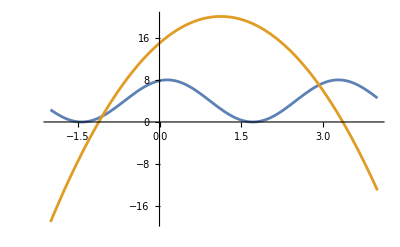

```mathematica
Plot[{f[x],g[x]},{x,-2,4}, AxesOrigin->{0,0}]
```

Корни находятся на промежутках (-1.5, -0.9) (2.8, 3.3)

МЕТОД НЬЮТОНА

```mathematica
a=-1.5; 
b=-0.9;
e = 0.001;
x1=a;
f2[x_]= 8*Cos[x+3]^2-15-9x+4 x^2;
Do[x2 = x1;
x1 = (x1-f2[x1]/f2'[x1])//N;
If [Abs[x2-x1]<e,
Print["Решение х = ",x2//N," получено на ",n," шаге."];
Break[]],
{n,1,100}
]
```

Решение х = -1.05372 получено на 4 шаге.

МЕТОД СЕКУЩИХ

```mathematica
a=-1.5; 
b=-0.9;
e = 0.001;
x1 = a;
f3[x_]=8*Cos[x+3]^2-15-9x+4 x^2;
x2= b;
Do[
x3= x2;
x2=x2-(x2-x1)/(f3[x2]-f3[x1])*f3[x2]//N;
If[Abs[x3-x2]< e,
Print["Решение x = ",x3//N, " получено на ",n, " шаге."];
Break[]],
{n,1,100}
]
```

Решение x = -1.05246 получено на 5 шаге.

### Задание 4: -Graphics- -Graphics-

МЕТОД ПРОСТЫХ ИТЕРАЦИЙ

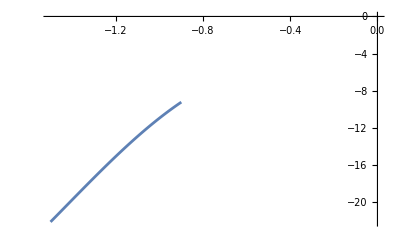

Решение x = -1.05545 получено на 7 шаге.

```mathematica
Clear[x,x1,x3];
f4[x_]=8*Cos[x+3]^2-15-9x+4 x^2;
f4Prime[x_]=D[f4[x],x];
Plot[f4Prime[x],{x,-1.5,-0.9},AxesOrigin->{0,0}]
x1=-1.5;x3=-0.9;n=0;e=0.001;
M=f4Prime[x1];
λ=1/M//N;
While[Abs[(x3-x1)]>e,x3=x1;
φ[x_]=x-λ*f4[x1]//N;
x1=φ[x1]//N;n++;]
Print["Решение x = ",x3//N," получено на ",n," шаге."];
```

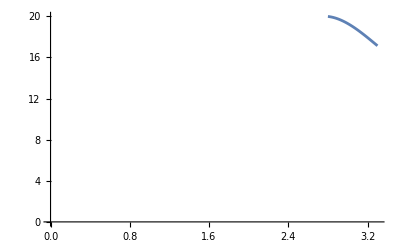

Решение x = 2.92845 получено на 2 шаге.

```mathematica
Clear[x,x1,x3];
f4[x_]=8*Cos[x+3]^2-15-9x+4 x^2;
f4Prime[x_]=D[f4[x],x];
Plot[f4Prime[x],{x,2.8,3.3},AxesOrigin->{0,0}]
x1=2.8;x3=3.3;n=0;e=0.001;
M=f4Prime[x1];
λ=1/M//N;
While[Abs[(x3-x1)]>e,x3=x1;
φ[x_]=x-λ*f4[x1]//N;
x1=φ[x1]//N;n++;]
Print["Решение x = ",x3//N," получено на ",n," шаге."];
```

### Задание 5: -Graphics- -Graphics-

```mathematica
fn[x_]:=8*Cos[x+3]^2
gn[x_]:=15+9x-4 x^2 
solutions=Solve[fn[x]==gn[x]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[8 Cos[3+x]^2==15+9 x-4 x^2]

Система результатов не может быть решена с помощью Solve

```mathematica
NSolve[fn[x]==gn[x]]
```

{{x→-1.05366},{x→-4.15698+2.03331 ⅈ},{x→-4.15698-2.03331 ⅈ},{x→-7.41198+2.51088 ⅈ},{x→-10.6113+2.82504 ⅈ},{x→-7.41198-2.51088 ⅈ},{x→-0.222198-1.09987 ⅈ},{x→2.92936},{x→-0.222198+1.09987 ⅈ},{x→4.24607-1.49761 ⅈ},{x→7.63593-2.24234 ⅈ},{x→7.63593+2.24234 ⅈ},{x→4.24607+1.49761 ⅈ},{x→-13.7896+3.06154 ⅈ},{x→10.862-2.64078 ⅈ},{x→-16.9571+3.25181 ⅈ}}

```mathematica
FindRoot[fn[x]==gn[x],{x,-1.5}]
```

{x→-1.05366}

```mathematica
FindRoot[fn[x]==gn[x],{x,-0.9}]
```

{x→-1.05366}

### Задание 6: -Graphics- -Graphics-

```mathematica
f[x_,x_]=((x-1)^2)^(1/3) + ((y-3)^2)^(1/3) -5
g[x_,y_]= √(x^2+y^2)- 2*Cosh[x-y-1]
```

-5+((-1+x)^2)^(1/3)+((-3+y)^2)^(1/3)

√(x^2+y^2)-2 Cosh[1-x+y]

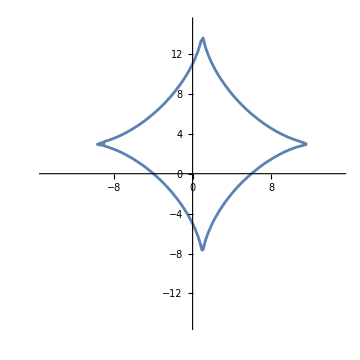

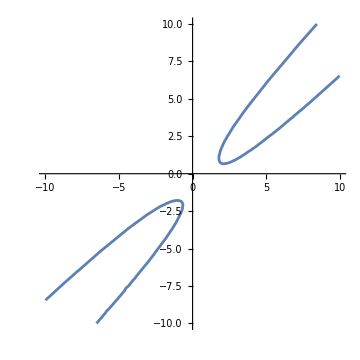

```mathematica
ggr1= ContourPlot[f[x,y]==0, {x,-15,15},{y,-15,15}, Axes->True, Frame->False,ImageSize->Medium]

ggr2=ContourPlot[g[x,y]==0,{x,-10,10},{y,-10,10},Axes->True,Frame->False,ImageSize->Medium]
```

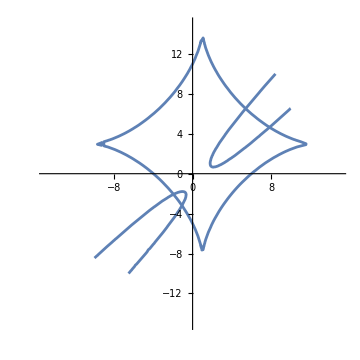

```mathematica
Show[ggr1, ggr2, ImageSize->Medium]
```

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0},{x,5},{y,6}]
```

{x→5.4,y→6.52196}

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0},{x,5},{y,8}]
```

{x→5.4,y→6.52196}

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0},{x,-2},{y,-2}]
```

{x→-1.94146,y→-2.05923}

```mathematica
FindRoot[{f[x,y]==0, g[x,y]==0},{x,-1},{y,-3}]
```

{x→-1.07866,y→-3.18993}